# Jakub Zbrzezny Numer indeksu: 286689 Numer na liście obecności: 1

## Zadanie 1 (a)

Mamy równanie różniczkowe x’’ + x’ + 8 x = -1 z warunkami początkowymi x(0) = 1 i x’(0) = 0. Oznaczmy to równanie (*).
Żeby sprowadzić równanie (*) do układu równań pierwszego rzędu bierzemy funkcję y(t) = x’(t). Mamy y’ = x’’= - x’ - 8 x - 1 oraz warunki początkowe: x(0) = 1, y(0) = 0. 
Równanie (*) jest spełnione wtedy i tylko wtedy, gdy :
{
	x’(t) = y(t),
	y’(t) = - y(t) - 8 x(t) - 1
}.
Oznaczmy ten układ (#).

```mathematica
f1[x_, y_]:=y;
```

```mathematica
f2[x_,y_]:=-y - 8x -1;
```

```mathematica
sol =DSolve[{x'[t]==f1[x[t],y[t]],y'[t]==f2[x[t],y[t]],x[0]==1,y[0]==0},{x[t],y[t]},t]
```

{{x[t]→-1/248 ⅇ^(-t/2) (-279 Cos[(√31 t)/2]+31 ⅇ^(t/2) Cos[(√31 t)/2]^2-9 √31 Sin[(√31 t)/2]+31 ⅇ^(t/2) Sin[(√31 t)/2]^2),y[t]→-(18 ⅇ^(-t/2) Sin[(√31 t)/2])/(√31)}}

```mathematica
FullSimplify[%]
```

{{x[t]→-1/8+9/248 ⅇ^(-t/2) (31 Cos[(√31 t)/2]+√31 Sin[(√31 t)/2]),y[t]→-(18 ⅇ^(-t/2) Sin[(√31 t)/2])/(√31)}}

Widzimy, że powyższe funkcje są rozwiązaniami układu (#).

Teraz narysujemy wykresy rozwiązań tego układu.

```mathematica
solutions=Evaluate[{x[t],y[t]}/.sol[[1]]];
```

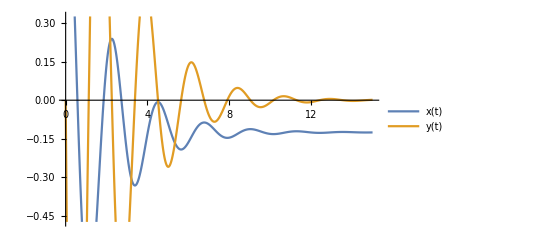

```mathematica
Plot[solutions,{t,0,15},PlotLegends->{"x(t)","y(t)"}]
```

Narysujemy wykres parametryczny rozwiązań (#) na tle portretu fazowego.
Portret fazowy ma kolor niebieski.
Wykres parametryczny ma kolor zielony.

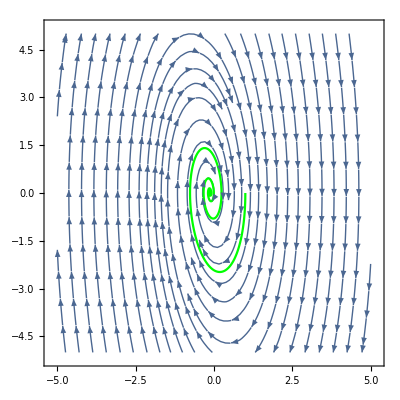

```mathematica
Show[
StreamPlot[{f1[x,y],f2[x,y]},{x,-5,5},{y,-5,5}],
ParametricPlot[solutions,{t,0,15},PlotStyle->Green]
]
```

## Zadanie 2 (b)

Mamy układ równań równań różniczkowych:
{
	x’ = 4 x - x^2 - 4 x y,
	y’ = 3 y - y^2 - x y
}.
Oznaczmy go (*).

Szukamy punktów równowagi układu (*), rozwiązując układ równań:
{ 
	4 x - x^2 - 4 x y = 0,
	3 y - y^2 - x y = 0
}
za pomocą funkcji Solve.

```mathematica
f1[x_,y_]:=4 x - x^2 - 4 x y;
```

```mathematica
f2[x_,y_]:=3 y - y^2 - x y;
```

```mathematica
Solve[{f1[x,y] == 0, f2[x,y] == 0}, {x, y}]
```

{{x→0,y→3},{x→8/3,y→1/3},{x→4,y→0},{x→0,y→0}}

Powyższe punky na płaszczyźnie są punkami równowagi (*).

Rozważymy dwa punkty równowagi (*) znajdujące się na osiach układu współrzędnych:
a) (x, y) = (0, 3), b) (x,y) = (4,0).

Dobieramy nietrywialny warunek początkowy, tak aby pierwsze rozwiązanie układu (*) (przy danych warunkach) zbiegało do (0,3), a drugie rozwiązanie do (4,0).
W tym celu narysujemy portret fazowy układu(*), żeby sprawdzić jakie powinny być warunki początkowe.
Żeby rozwiązanie (*) zbiegało do (0,3) (do (4,0)), to trzeba wziąć warunek początkowy taki, że portret fazowy od warunku początkowego prowadził  (x(t),y(t)) do (0,3) (do (4,0)).

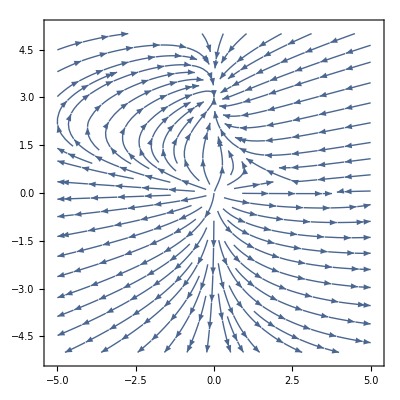

```mathematica
StreamPlot[{f1[x,y],f2[x,y]}, {x,-5,5},{y,-5,5}]
```

a) (x,y)=(0,3)
Widzimy, że x(0) = - 0.1 , y(0) = 0.1 spełniają warunki zbieżności rozwiązania (x(t), y(t)) do (0,3).

```mathematica
sola = NDSolve[{x'[t] == f1[x[t],y[t]], y'[t] == f2[x[t],y[t]], x[0]==-0.1,y[0]==0.1}, {x[t],y[t]}, {t,-10,15}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

```mathematica
solutionsa=Evaluate[{x[t],y[t]}/.sola[[1]]];
```

b) (x, y) = (4, 0)
Widzimy, że x(0) = 1/2 , y(0) = - 0.1 spełniają warunki zbieżności rozwiązania (x(t),y(t)) do (4,0).

```mathematica
solb = NDSolve[{x'[t] ==f1[x[t],y[t]], y'[t] == f2[x[t],y[t]], x[0]==1/2,y[0]==-0.1}, {x[t],y[t]}, {t,-10,15}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

```mathematica
solutionsb=Evaluate[{x[t],y[t]}/.solb[[1]]];
```

Teraz nanosimy wykresy uzyskanych rozwiązań na portret fazowy układu (*).

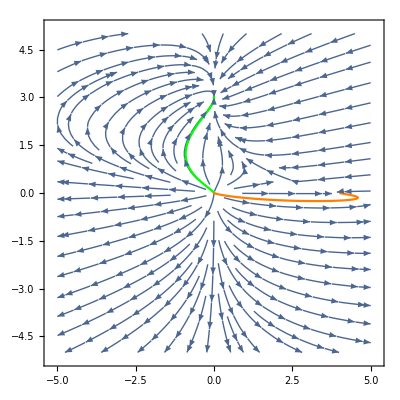

```mathematica
Show[
StreamPlot[{f1[x,y], f2[x,y]}, {x,-5,5},{y,-5,5}],
ParametricPlot[solutionsa,{t,-10,15}, PlotStyle->Green],
ParametricPlot[solutionsb,{t,-10,15}, PlotStyle->Orange]

]
```

## Zadanie 3 (a)

Mamy układ równań różniczkowych: 
{
	x’ = -3x +3y,
	y’ = -2x +2y
}.	
Oznaczmy go (*).
Układ (*) jest spełniony wtedy i tylko wtedy, gdy ((x, (y))^T)’=A (x,y)^T, gdzie A jest stałą macierzą wymiaru 2x2.
Widzimy, że A = (-3 | 3
-2 | 2).

```mathematica
A={{-3,3},{-2,2}};
```

```mathematica
eigval=Eigenvalues[A]
```

{-1,0}

```mathematica
eigvec=Eigenvectors[A]
```

{{3,2},{1,1}}

Skoro macierz A ma 2 różne rzeczywiste wartości własne, macierz fundamentalna układu (*) ma postać:

```mathematica
Φ=Transpose[{eigvec[[1]] * Exp[eigval[[1]]*t],eigvec[[2]] * Exp[eigval[[2]]*t]}];
```

```mathematica
Φ//MatrixForm
```

(3 ⅇ^-t | 1
2 ⅇ^-t | 1)

Teraz za pomocą tej macierzy, rozwiązując układ ((x(t), (y(t)))^T)’=A (x(t),y(t))^T, szukamy rozwiązań zagadnienia początkowego dla warunków początkowych: x(0) = 1, y(0) =−1.

```mathematica
c=Inverse[Φ/.t-> 0].{1,-1}
```

{2,-5}

```mathematica
Φ.c
```

{-5+6 ⅇ^-t,-5+4 ⅇ^-t}

Rozwiązaniami x(t), y(t) są odpowiednio pierwszy element wektora powyżej, drugi element wektora powyżej.

Sprawdzimy, czy wynik jest poprawny za pomocą funkcji DSolve.

```mathematica
Expand[DSolve[{{x'[t],y'[t]}==A.{x[t],y[t]},x[0]==1,y[0]==-1},{x[t],y[t]},t]]
```

{{x[t]→-5+6 ⅇ^-t,y[t]→-5+4 ⅇ^-t}}

Zatem wynik jest poprawny.

## Zadanie 4 (b)

Mamy macierz A = (1 | -2
-1 | -5).

```mathematica
A = {{1,-2},{-1,-5}};
```

```mathematica
Φ=MatrixExp[A t];
```

Macierzą e^(A t) jest macierz:

```mathematica
Φ//MatrixForm
```

(1/2 ⅇ^(-2 t-√11 t)-(3 ⅇ^(-2 t-√11 t))/(2 √11)+1/2 ⅇ^(-2 t+√11 t)+(3 ⅇ^(-2 t+√11 t))/(2 √11) | ⅇ^(-2 t-√11 t)/(√11)-ⅇ^(-2 t+√11 t)/(√11)
ⅇ^(-2 t-√11 t)/(2 √11)-ⅇ^(-2 t+√11 t)/(2 √11) | 1/2 ⅇ^(-2 t-√11 t)+(3 ⅇ^(-2 t-√11 t))/(2 √11)+1/2 ⅇ^(-2 t+√11 t)-(3 ⅇ^(-2 t+√11 t))/(2 √11))

Teraz porównamy otrzymany wynik z przybliżeniem uzyskanym przez wysumowanie 8 pierwszych wyrazów rozwinięcia e^(A t) w szereg Taylora (umieszczając funkcje znajdujące się w poszczególnych komórkach macierzy na wykresach).

```mathematica
S =Normal[Series[Φ,{t,0,7}]]
```

{{1+t+(3 t^2)/2-(5 t^3)/6+(41 t^4)/24-(199 t^5)/120+(361 t^6)/240-(1145 t^7)/1008,-2 t+4 t^2-(23 t^3)/3+10 t^4-(641 t^5)/60+(851 t^6)/90-(18103 t^7)/2520},{-t+2 t^2-(23 t^3)/6+5 t^4-(641 t^5)/120+(851 t^6)/180-(18103 t^7)/5040,1-5 t+(27 t^2)/2-(143 t^3)/6+(761 t^4)/24-(809 t^5)/24+(7169 t^6)/240-(114343 t^7)/5040}}

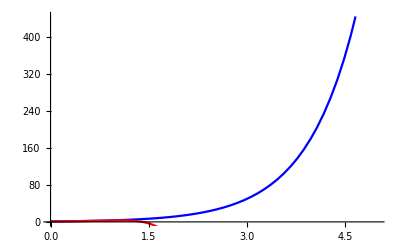

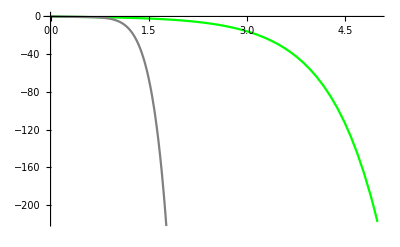

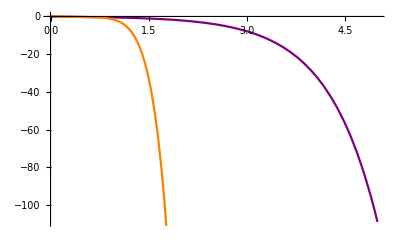

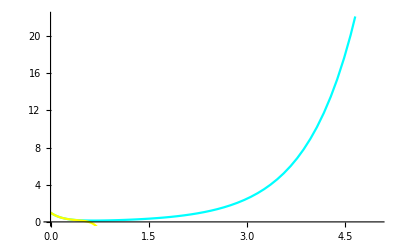

```mathematica
Show[
Plot[Φ[[1,1]], {t,0,5}, PlotLegends->"Φ[[1,1]]-Blue", PlotStyle->Blue], 
Plot[S[[1,1]], {t,0,5}, PlotLegends->"S[[1,1]]-Red", PlotStyle->Red]
]
Show[
Plot[Φ[[1,2]], {t,0,5}, PlotLegends->"Φ[[1,2]]-Green", PlotStyle->Green],
Plot[S[[1,2]], {t,0,5},PlotLegends->"S[[1,2]]-Gray", PlotStyle->Gray]
]
Show[
Plot[Φ[[2,1]], {t,0,5}, PlotLegends->"Φ[[2,1]]-Purple", PlotStyle->Purple],
Plot[S[[2,1]], {t,0,5}, PlotLegends->"S[[2,1]]-Orange", PlotStyle->Orange]
]
Show[
Plot[Φ[[2,2]], {t,0,5}, PlotLegends->"Φ[[2,2]]-Cyan", PlotStyle->Cyan],
Plot[S[[2,2]], {t,0,5}, PlotLegends->"S[[2,2]]-Yellow", PlotStyle->Yellow]
]
```

Widzimy, że przybliżenie uzyskane przez wysumowanie 8 pierwszych wyrazów rozwinięcia e^(A t) w szereg Taylora odbiega od otrzymanego wyniku.
Czyli przybliżenie nie jest dokładne.